```mathematica
Quit[]
```

### Problem 2

```mathematica
re = 6378 Kilometers(*/.Kilometers-> am/384400/.am->1*);
r0 = re+200Kilometers/.Kilometers-> am/384400/.am->1;
r1 = 386338 Kilometers/.Kilometers-> am/384400/.am->1;
μe=398600.4418 Kilometers^3/Seconds^2/.Kilometers-> am/384400/.Seconds-> day/(24*60*60)/.am->1/.day->1;
μm=4902.8 Kilometers^3/Seconds^2/.Kilometers-> am/384400/.Seconds-> day/(24*60*60)/.am->1/.day->1;
ahof = (r0+r1)/2;
am=1;
vbeforetrans = √(μe(2/r0-1/r0));
vaftertrans =√(μe(2/r0-1/ahof))//N;
inix=-r0;
iniy = 0;
inivx = 0;
inivy = -vaftertrans;
```

### Part a

```mathematica
vaftertrans aam/day/.aam->384400 km/.day->24*60*60 s
```

(10.9162 km)/s

### Part b

```mathematica
transfer=NDSolve[{x''[t]==-μe/((x[t]^2+y[t]^2)^(3/2))x[t],y''[t]==-μe/((x[t]^2+y[t]^2)^(3/2))y[t],x[0]==inix,y[0]==iniy,x'[0]==inivx,y'[0]==inivy},{x,y},{t,0,7}][[1]];
```

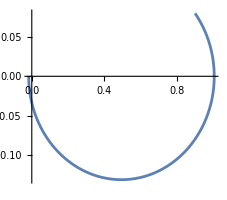

```mathematica
ParametricPlot[{x[t],y[t]}/.transfer,{t,0,7}]
```

```mathematica
tenc =FindRoot[(x[t]^2+y[t]^2/.transfer)==r1^2,{t,5,0,7}][[1,2]];
nm = √(μm/am^3);
 θtenc = ArcTan[x[tenc],y[tenc]]/.transfer;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
θt0 = θtenc-nm tenc
```

```mathematica
θm[t_]:=θt0+nm t
xm[t_]:= am Cos[θm[t]]
ym[t_]:= am Sin[θm[t]]
```

```mathematica
F[x_,y_,t_]:=-μe/((x^2+y^2)^(3/2)){x,y}+μm(({xm[t],ym[t]}-{x,y})/Norm[{xm[t],ym[t]}-{x,y}]^3-{xm[t],ym[t]}/Norm[{xm[t],ym[t]}]^3)
```

```mathematica
trajectory=ParametricNDSolve[{x''[t]==F[x[t],y[t],t][[1]] ,y''[t]==F[x[t],y[t],t][[2]],x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,10},{x0,y0,vx0,vy0}];
```

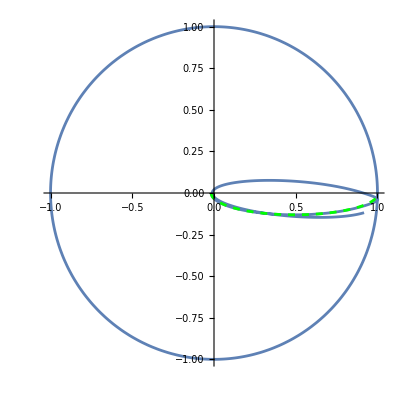

```mathematica
pfull=ParametricPlot[{x[inix,iniy,inivx,inivy][t],y[inix,iniy,inivx,inivy][t]}/.trajectory,{t,0,10},AspectRatio->1,PlotRange->{{-1,1},{-1,1}}];
ptransfer=ParametricPlot[{x[t],y[t]}/.transfer,{t,0,tenc},AspectRatio->1,PlotStyle->Directive[Dashed,Green]];
pmoon=ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2π}];
Show[pfull,ptransfer,pmoon]
```

#### STM numerical solution

```mathematica
f[x_,y_,vx_,vy_,t_]:= {vx,vy,F[x,y,t]}//Flatten
αs={x,y,vx,vy};
A[x_,y_,vx_,vy_,t_]:=Evaluate[Table[D[f[x,y,vx,vy,t][[i]],α],{i,1,4},{α,αs}]/.{Abs'[z_]Abs[z_]->z}]
```

```mathematica
Φ=Table[ToExpression["ϕ"<>ToString[i]<>ToString[j]<>"[t]"],{i,4},{j,4}];
Φ0=Table[ToExpression["ϕ"<>ToString[i]<>ToString[j]<>"[0]"],{i,4},{j,4}];
dΦdt=Table[ToExpression["ϕ"<>ToString[i]<>ToString[j]<>"'[t]"],{i,4},{j,4}];
unknowns =Table[ToExpression["ϕ"<>ToString[i]<>ToString[j]],{i,4},{j,4}]//Flatten;
```

```mathematica
stmeq[x0_,y0_,vx0_,vy0_]:=(#==0)&/@Flatten[dΦdt-(A[x[x0,y0,vx0,vy0][t],y[x0,y0,vx0,vy0][t],x[x0,y0,vx0,vy0]'[t],y[x0,y0,vx0,vy0]'[t],t]/.trajectory).Φ]
stmic = (#==0)&/@Flatten[Φ0-IdentityMatrix[4]];
stmfull[x0_,y0_,vx0_,vy0_]:=Join[stmeq[x0,y0,vx0,vy0],stmic]
```

```mathematica
stm[x0_?NumericQ,y0_?NumericQ,vx0_?NumericQ,vy0_?NumericQ,tf_?NumericQ]:=ArrayReshape[Through[NDSolve[stmfull[x0,y0,vx0,vy0],unknowns,{t,0,tf}][[1]][[All,2]][tf]],{4,4}]
```

```mathematica
stm[inix,iniy,inivx,inivy,0.0000000001]//MatrixForm
```

(1. | -3.84979×10^-25 | 1.×10^-10 | -3.1161×10^-37
-3.84979×10^-25 | 1. | -3.1161×10^-37 | 1.×10^-10
2.09081×10^-6 | -2.79941×10^-16 | 1. | 3.68219×10^-25
-2.79941×10^-16 | -1.0454×10^-6 | 3.68219×10^-25 | 1.)

```mathematica
αs={x0,y0,vx0,vy0};
fs={x,y,x',y'};
tf=7;
ϵ=10^-10;
pervecs=ϵ{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
x00=inix;
y00=iniy;
vx00=inivx;
vy00=inivy;
STMfindiffrows12=Evaluate[Table[1/ϵ(f[x00+pv[[1]],y00+pv[[2]],vx00+pv[[3]],vy00+pv[[4]]][tf]-f[x00,y00,vx00,vy00][tf])/.trajectory,{f,fs[[1;;2]]},{pv,pervecs}]];
STMfindiffrows34=Evaluate[Table[1/ϵ(f[x00+pv[[1]],y00+pv[[2]],vx00+pv[[3]],vy00+pv[[4]]]'[tf]-f[x00,y00,vx00,vy00]'[tf])/.trajectory,{f,fs[[1;;2]]},{pv,pervecs}]];
STMfindiff=Join[STMfindiffrows12,STMfindiffrows34];
STMfull=stm[x00,y00,vx00,vy00,tf];
STMfindiff/STMfull//TableForm
```

0.999801 | 1.00002 | 1.0001 | 0.999901
1.00026 | 1.00021 | 1.00242 | 1.00011
0.999563 | 1.00003 | 1.00033 | 0.999834
0.999932 | 1. | 0.999941 | 0.999982

#### Sensitivity matrix

```mathematica
cosα[x0_,y0_,vx0_,vy0_,t_]:={x[x0,y0,vx0,vy0][t],y[x0,y0,vx0,vy0][t]}.{x[x0,y0,vx0,vy0]'[t],y[x0,y0,vx0,vy0]'[t]}/(Norm[{x[x0,y0,vx0,vy0][t],y[x0,y0,vx0,vy0][t]}]*Norm[{x[x0,y0,vx0,vy0]'[t],y[x0,y0,vx0,vy0]'[t]}])
γ[x0_,y0_,vx0_,vy0_,t_]:= ArcCos[cosα[x0,y0,vx0,vy0,t]]-90 Degree
```

```mathematica
rd = (92+ 6378) Kilometers/.Kilometers-> am/384400/.am->1;
γd=-7.5Degree;
αd=90 Degree+γd;
cosαd=Cos[αd];
```

```mathematica
error[x0_,y0_,vx0_,vy0_,t_]:={Norm[{x[x0,y0,vx0,vy0][t],y[x0,y0,vx0,vy0][t]}]-rd,γ[x0,y0,vx0,vy0,t]-γd}
```

```mathematica
shit=({{(x Φ13+y Φ23)/r, ((vx^2 (y Φ13-x Φ23)+vy (vy y Φ13-vy x Φ23-r^2 Φ33)+r^2 vx Φ43) Sign[vy x-vx y])/(r^2 v^2)}, {(x Φ14+y Φ24)/r, ((vx^2 (y Φ14-x Φ24)+vy (vy y Φ14-vy x Φ24-r^2 Φ34)+r^2 vx Φ44) Sign[vy x-vx y])/(r^2 v^2)}})//Transpose;
```

```mathematica
stmrepl2[x0_,y0_,vx0_,vy0_,t_]:={
x->x[x0,y0,vx0,vy0][t],
y->y[x0,y0,vx0,vy0][t],
vx->x[x0,y0,vx0,vy0]'[t],
vy->y[x0,y0,vx0,vy0]'[t],
r->Norm[{x[x0,y0,vx0,vy0][t],y[x0,y0,vx0,vy0][t]}],
v->Norm[{x[x0,y0,vx0,vy0]'[t],y[x0,y0,vx0,vy0]'[t]}],
Φ13->stm[x0,y0,vx0,vy0,t][[1,3]],
Φ14->stm[x0,y0,vx0,vy0,t][[1,4]],
Φ23->stm[x0,y0,vx0,vy0,t][[2,3]],
Φ24->stm[x0,y0,vx0,vy0,t][[2,4]],
Φ33->stm[x0,y0,vx0,vy0,t][[3,3]],
Φ34->stm[x0,y0,vx0,vy0,t][[3,4]],
Φ43->stm[x0,y0,vx0,vy0,t][[4,3]],
Φ44->stm[x0,y0,vx0,vy0,t][[4,4]]
};
```

```mathematica
tf=7.88;
Sensm[x0_,y0_,vx0_,vy0_,t_]:=shit/.stmrepl2[x0,y0,vx0,vy0,t]/.trajectory
invsensm[x0_,y0_,vx0_,vy0_,t_]:= Inverse[Sensm[x0,y0,vx0,vy0,t]]
invsensm0[{vx0_,vy0_}]:=invsensm[inix,iniy,vx0,vy0,tf]
error0[{vx0_,vy0_}]:=error[inix,iniy,vx0,vy0,tf]/.trajectory
```

#### Finding the correction

```mathematica
n=100;
param = 0.1;
XState=ConstantArray[0,n];
ERR=ConstantArray[0,n];
B=ConstantArray[0,n];
XState[[1]] = {inivx,inivy};
ERR[[1]]=error0[XState[[1]]];
B[[1]]=invsensm0[XState[[1]]];
Dynamic[i]
```

```mathematica
For[i=1,i<n,i++,
XState[[i+1]]=XState[[i]]-param (B[[i]].ERR[[i]]);
ERR[[i+1]]=error0[XState[[i+1]]];
B[[i+1]]=invsensm0[XState[[i+1]]];
]
```

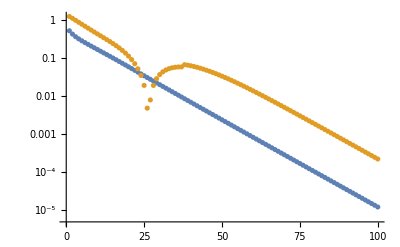

```mathematica
ListLogPlot[ERR//Transpose//Abs]
```

```mathematica
errordata=ParallelTable[{vx0,vy0,error0[{vx0,vy0}]}//Flatten//Chop,{vx0,-0.05,0.05,0.001},{vy0,-4.26,-4.14,0.0005}];
errordata=ArrayReshape[errordata,{Dimensions[errordata][[1]]*Dimensions[errordata][[2]],Dimensions[errordata][[3]]}];
errornormdata=Transpose[{errordata[[All,1]],errordata[[All,2]],Norm/@errordata[[All,{3,4}]]}];
```

```mathematica
d1=ListDensityPlot[errordata[[All,{1,2,3}]],PlotLegends->Automatic,PlotRange->All];
d2=ListDensityPlot[errordata[[All,{1,2,4}]],PlotLegends->Automatic,PlotRange->All];
c1=ListContourPlot[errordata[[All,{1,2,3}]],PlotLegends->Automatic,Contours->{0},ContourShading->None];
c2=ListContourPlot[errordata[[All,{1,2,4}]],PlotLegends->Automatic,Contours->{0},ContourShading->None];
dnorm=ListDensityPlot[errornormdata,PlotLegends->Automatic];
p1=Show[d1,c1]
p2=Show[d2,c2]
pnorm=Show[dnorm,c1,c2]
```

```mathematica
Dynamic[normerr]
```

```mathematica
XStateold = {inivx,inivy};
ERRold=error0[XStateold];
Aold=invsensm0[XStateold];
normerr = 1;
While[normerr>10^-6,
XStatenew=XStateold-param (Aold.ERRold);
ERRnew=error0[XStatenew];
Anew=invsensm0[XStatenew];
normerr = Norm[ERRnew];
XStateold = XStatenew;
ERRold = ERRnew;
Aold=Anew;
]
```

```mathematica
ΔV= XStatenew - {inivx,inivy}
```

{-0.0642606,0.000940606}

```mathematica
vxcorr=ΔV[[1]] amm/day/.amm->384400 km/.day->24*60*60 s
vycorr = ΔV[[1]] amm/day/.amm->384400 km/.day->24*60*60 s
```

-(0.2859 km)/s

-(0.2859 km)/s

```mathematica
{vxcorr,vycorr}
```

{-(0.2859 km)/s,-(0.2859 km)/s}